```mathematica
ϕ0 [r_]:=2r-1
```

```mathematica
ϕi[r_,i_]:=(r-1)*(6-r)^i
```

```mathematica
dϕi[r_,i_]:=ϕi'[r,i]
```

```mathematica
c := {c1, c2, c3, c4, c5, c6, c7, c8}
```

```mathematica
u[r_]:=ϕ0[r] + Sum[c[[i]]*ϕi[r,i],{i,1,8}]
```

```mathematica
du [r_]:=u'[r]
```

```mathematica
du[r]
```

2+c1 (6-r)+c2 (6-r)^2+c3 (6-r)^3+c4 (6-r)^4+c5 (6-r)^5+c6 (6-r)^6+c7 (6-r)^7+c8 (6-r)^8-c1 (-1+r)-2 c2 (6-r) (-1+r)-3 c3 (6-r)^2 (-1+r)-4 c4 (6-r)^3 (-1+r)-5 c5 (6-r)^4 (-1+r)-6 c6 (6-r)^5 (-1+r)-7 c7 (6-r)^6 (-1+r)-8 c8 (6-r)^7 (-1+r)

```mathematica
B[j_]:=Integrate[r^2*dϕi[r,j]*du[r]-r*ϕi[r,j]*du[r]+ϕi[r,j]*u[r]*(r^4+4),{r,1,6}]
```

```mathematica
B[1]
```

1/144144 125 (48317412+26672360 c1+45369610 c2+93672800 c3+221978250 c4+583643750 c5+1664937500 c6+5072437500 c7+16314140625 c8)+432 (1+332563968 c8) ϕi'[System`ComplexExpandDump`d$831917[1]]-2 (1+198 c8) ϕi'[System`ComplexExpandDump`d$832018[1]]

```mathematica
B1 :=1/144144 125 (48317412+26672360 c1+45369610 c2+93672800 c3+221978250 c4+583643750 c5+1664937500 c6+5072437500 c7+16314140625 c8)
```

```mathematica
B[2]
```

```mathematica
B2:=1/2450448 625 (209304238+152827246 c1+315278600 c2+746339100 c3+1960078750 c4+5584818750 c5+16994900000 c6+54597890625 c7+183547031250 c8)
```

```mathematica
B[3]
```

```mathematica
B3=1/2450448 625 (360142926+312069680 c1+737952150 c2+1935768750 c3+5508850000 c4+16743512500 c5+53727703125 c6+180423281250 c7+629697265625 c8)
```

1/2450448 625 (360142926+312069680 c1+737952150 c2+1935768750 c3+5508850000 c4+16743512500 c5+53727703125 c6+180423281250 c7+629697265625 c8)

```mathematica
B[4]
```

```mathematica
B4=1/46558512 3125 (2855420776+2772347760 c1+7263543250 c2+20644948750 c3+62670075000 c4+200858559375 c5+673738218750 c6+2348941796875 c7+8465187500000 c8)
```

1/46558512 3125 (2855420776+2772347760 c1+7263543250 c2+20644948750 c3+62670075000 c4+200858559375 c5+673738218750 c6+2348941796875 c7+8465187500000 c8)

```mathematica
B[5]
```

```mathematica
B5=1/46558512 78125 (273153348+286846610 c1+814250700 c2+2468592100 c3+7902073875 c4+26474718750 c5+92201359375 c6+331945625000 c7+1229895390625 c8)
```

```mathematica
(26474718750*78125)*1/46558512
```

```mathematica
N[18143310546875/408408]
```

4.44245×10^7

```mathematica
B[6]
```

```mathematica
B6=1/46558512 390625 (144753096+160540690 c1+486076240 c2+1553961075 c3+5199981750 c4+18089009375 c5+65056750000 c6+240816125000 c7+914071640625 c8)
```

```mathematica
N[914071640625*390625/46558512]
```

7.66904×10^9

```mathematica
B[7]
```

```mathematica
B7=1/46558512 1953125 (95686812 c1+25 (3324316+12220059 c2+40840158 c3+141901975 c4+509795000 c5+1885225375 c6+7149553125 c7+27719818750 c8))
```

1/46558512 1953125 (95686812 c1+25 (3324316+12220059 c2+40840158 c3+141901975 c4+509795000 c5+1885225375 c6+7149553125 c7+27719818750 c8))

```mathematica
B[8]
```

```mathematica
B8=1/1070845776 1953125 (5852447336+6904846905 c1+23046265650 c2+79977828125 c3+287003200000 c4+1060255006250 c5+4017256546875 c6+15562973359375 c7+61482890625000 c8)
```

1/1070845776 1953125 (5852447336+6904846905 c1+23046265650 c2+79977828125 c3+287003200000 c4+1060255006250 c5+4017256546875 c6+15562973359375 c7+61482890625000 c8)

```mathematica
L[j_]:=(6^2*ϕi[6,j]*du[6]) - (1^2*ϕi[1,j]*du[1])-Integrate[16*r*Cos[Pi*r]*ϕi[r,j],{r,1,6}]
```

```mathematica
L[1]
```

-(192-400 π^2)/π^4

```mathematica
N[L[3]]
```

-287.346

```mathematica
BB:={B1,B2,B3,B4,B5,B6,B7,B8}
```

```mathematica
LL:={L[1],L[2],L[3],L[4],L[5],L[6],L[7],L[8]}
```

```mathematica
Solve[BB==LL,c]
```

{{c1→-1/(23453464857650557347656738907607689494140625 π^10)2 (-176015441814833171328975099031859147818242146304+517900352522807838983332765425524510853527654400 π^2-189268338494223236956302903353762480526322560000 π^4+17261637514741737381614489535021054613984800000 π^6-294058587528609155478427032998590444020000000 π^8+290625396673353240807641386898044428983984375 π^10),c2→1/(117267324288252786738283694538038447470703125 π^10)34 (-320151363685084898855911785635355827217052827648+941442799325985793841442766079856662522764800000 π^2-342646651996728881846104389422953568250622080000 π^4+30881447890050803888734548402946324254530400000 π^6-508892703801396527329885153281731214780000000 π^8+300178610441913095161179529947655613950390625 π^10),c3→-1/(586336621441263933691418472690192237353515625 π^10)238 (-485585046399335333404974870479512678460400992256+1427848977456475466380420663442466386264631398400 π^2-519503845870480814938082569835514321922458240000 π^4+46786545223310750776160618880727944015952800000 π^6-771223863084788454365343243363717589740000000 π^8+343482139425811157106907766942840823516015625 π^10),c4→1/(2931683107206319668457092363450961186767578125 π^10)58786 (-9863790885738713642516400599293507472792420352+29013953072675883341450007878121040333040332800 π^2-10580928126425607348645444589385624059440000000 π^4+959221635751619187745499141235871275525600000 π^6-16087327554998700552575884677844606920000000 π^8+5886949247281298499441463463490064846484375 π^10),c5→-1/(14658415536031598342285461817254805933837890625 π^10)646 (-2385450341952453366305141762424329765011946274816+7021012431429681443074812075297231868603567718400 π^2-2571262347529520557180367088574119050740224000000 π^4+235788978709092512813098159978420282634764800000 π^6-4060803202035118264791714055258904712660000000 π^8+1274140199512439212320328105782247083935546875 π^10),c6→1/(14658415536031598342285461817254805933837890625 π^10)646 (-688602444132290220077825193218526328160941375488+2028386100214362675282191492893669203336226160640 π^2-746973603572304210549581134323542216026149120000 π^4+69514213447223539020763479363280053275481600000 π^6-1235819967801187717847422824097650364512000000 π^8+341050968718734192208102830680876563847265625 π^10),c7→-1/(73292077680157991711427309086274029669189453125 π^10)49742 (-6608140814123873221497594970105033525487075328+19483901134329878896903658111637732327393853440 π^2-7221739592132434939510095953310683641336320000 π^4+683473225858178225609511695212653298017600000 π^6-12580073583379869750015831613318876302000000 π^8+3105800542005167467179667148839959190234375 π^10),c8→1/(14658415536031598342285461817254805933837890625 π^10)59432 (-65429272749367664398041367121695749991514112+193119931807895519805636783567739886175866880 π^2-72090715213206647001002049721900183001088000 π^4+6947751701198533874732817484038524636400000 π^6-132613509347227122114273279082994317500000 π^8+29646639540853131549322218102692605578125 π^10)}}

```mathematica
N[%72]
```

{{c1→-25.0599,c2→88.4414,c3→-142.304,c4→121.333,c5→-58.3158,c6→15.8174,c7→-2.25239,c8→0.13057}}

```mathematica
{c1,c2,c3,c4,c5,c6,c7,c8}/.{{c1->-25.05994264464042,c2->88.44142184529755,c3->-142.303636583464,c4->121.33250556033146,c5->-58.31582261788433,c6->15.817431477722486,c7->-2.2523913507403646,c8->0.13056953836355073}}
```

{{-25.0599,88.4414,-142.304,121.333,-58.3158,15.8174,-2.25239,0.13057}}

```mathematica
c1=-25.05994264464042
c2=88.44142184529755
c3=-142.303636583464
c4=121.33250556033146
c5=-58.31582261788433
c6=15.817431477722486
c7=-2.2523913507403646
c8=0.13056953836355073
```

-25.0599

88.4414

-142.304

121.333

-58.3158

15.8174

-2.25239

0.13057

```mathematica
u[1]
```

1

```mathematica
u[2]
```

-1.86599

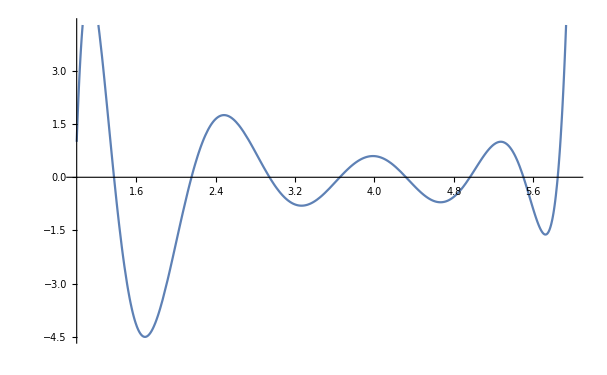

```mathematica
Plot[u[r],{r,1,6}]
```